### Generating data

```mathematica
hsgen[datasize_,ifci_,taylororder_:20,max_:{10,10,5}]:=Module[{hslist,counter,numfac,numdegs,num,denomdeg,hs,numexp,coeff},
hslist={};
counter=1;
While[counter≤datasize,
{
numfac=RandomInteger[{1,max[[1]]}];
numdegs=Table[RandomInteger[{1,max[[2]]}],{i,1,numfac}];
num=Times@@((1-t^#)&/@numdegs);
denomdeg=RandomInteger[{1,max[[3]]}]+Total[numdegs];
If[ifci[[counter]]==1,hs=num/(1-t)^denomdeg,If[Length[numdegs]>1,hs=(num+t^Min[numdegs]+(-1)^Length[numdegs] t^(-Min[numdegs]+Total[numdegs]))/(1-t)^denomdeg,hs=(1+t^Min[numdegs])/(1-t)^denomdeg]];
numexp=CoefficientList[Numerator[hs],t];
coeff=Series[hs,{t,0,taylororder}][[3]];
AppendTo[hslist,{hs,numexp,coeff,ifci[[counter]]}];
counter++;
}];
Return[hslist]]
```

```mathematica
hsgen[5,{1,1,0,0,1}]
```

{{((1-t^3) (1-t^4)^2)/(1-t)^16,{1,0,0,-1,-2,0,0,2,1,0,0,-1},{1,16,136,815,3858,15336,53176,165038,467091,1222520,2991456,6903325,15130596,31682288,63689616,123428636,231420133,421070400,745473816,1287195851,2172100726},1},{((1-t^2)^2 (1-t^3) (1-t^10)^2)/(1-t)^32,{1,0,-2,-1,1,2,0,-1,0,0,-2,0,4,2,-2,-4,0,2,0,0,1,0,-2,-1,1,2,0,-1},{1,32,526,5919,51273,364530,2214672,11820951,56561484,246354768,988504438,3689377268,12909426784,42627454026,133568671422,399029536800,1141196345538,3135520770114,8302363210356,21243517847742,52655034766291},1},{(t+t^10+(1-t) (1-t^10))/(1-t)^12,{1,0,0,0,0,0,0,0,0,0,0,1},{1,12,78,364,1365,4368,12376,31824,75582,167960,352716,705433,1352090,2496222,4457764,7727525,13042263,21486556,34629114,54702882,84840275},0},{(t^2+t^23+(1-t^2) (1-t^4) (1-t^9) (1-t^10))/(1-t)^30,{1,0,0,0,-1,0,1,0,0,-1,-1,1,1,1,1,-1,-1,0,0,1,0,-1,0,0,0,1},{1,30,465,4960,40919,278226,1622696,8342750,38567565,162738343,634163125,2303731522,7861664666,25364021936,77781509264,227760972214,639353867176,1726443088121,4497976485181,11336705064905,27706543608284},0},{((1-t^4)^2 (1-t^7)^2 (1-t^8) (1-t^9) (1-t^10)^2)/(1-t)^64,{1,0,0,0,-2,0,0,-2,0,-1,-2,4,2,2,5,0,1,4,-2,-2,-3,-10,-4,-3,-4,1,0,0,8,7,7,8,0,0,1,-4,-3,-4,-10,-3,-2,-2,4,1,0,5,2,2,4,-2,-1,0,-2,0,0,-2,0,0,0,1},{1,64,2080,45760,766478,10424000,119873312,1198683198,10637592552,85092152703,621085090846,4177423221380,26102590263202,152553809950066,838738461912453,4359533249326224,21514157504373509,101183069930237340,455015553486541246,1962249413266019358,8136365019166694533},1}}

```mathematica
dataset={};
```

```mathematica
n=15000;
dataset=Union[dataset,hsgen[n,{Table[1,{i,1,n/2}],Table[0,{i,1,n/2}]}//Flatten,100]];
Length[dataset]
Count[dataset[[;;,4]],0]
Count[dataset[[;;,4]],1]
```

11273

5903

5370

```mathematica
n=20;
dataset=Union[dataset,hsgen[n,Table[1,{i,1,n}],100]];
Length[dataset]
Count[dataset[[;;,4]],0]
Count[dataset[[;;,4]],1]
```

11803

5903

5900

#### Using numerator coefficients as input

```mathematica
data=Map[#[[2]]->#[[4]]&,dataset];
data=DeleteDuplicates[data];
Length[data]
```

9241

#### Using Taylor coefficients as input

```mathematica
data=Map[#[[3]]->#[[4]]&,dataset];
data=DeleteDuplicates[data];
Length[data]
```

11597

#### Export data

using numerator coefficients as input

```mathematica
rightpad[x_,n_]:=Block[{res,i},
res=Table[0,{i,1,n}];
Do[res[[i]]=x[[i]],{i,1,Length[x]}];
Return[res];
]
```

```mathematica
datanum=Map[{#[[2]],#[[4]]}&,dataset];
datanum=DeleteDuplicates[datanum];
Length[datanum]
```

9244

```mathematica
Max[Union[Length[#[[1]]]&/@datanum]]
```

85

```mathematica
datanumpad=rightpad[#[[1]],85]&/@datanum;
```

```mathematica
datanuminput=Map[{#}&,datanumpad];
Length[datanuminput]
datanumoutput=Map[#[[2]]&,datanum];
Length[datanumoutput]
```

9244

9244

using Taylor coefficients as input

```mathematica
datatay=Map[{#[[3]],#[[4]]}&,dataset];
datatay=DeleteDuplicates[datatay];
Length[datatay]
```

11597

```mathematica
datatayinput=Map[{#[[1]]}&,datatay];
Length[datatayinput]
datatayoutput=Map[#[[2]]&,datatay];
Length[datatayoutput]
```

11597

11597

```mathematica
Export["Directory Here",datanuminput];
Export["Directory Here",datanumoutput];
```

```mathematica
Export["Directory Here",datatayinput];
Export["Directory Here",datatayoutput];
```

### Machine Learning

#### k-fold cross validation

```mathematica
k=5;
subset={};
For[i=1,i≤k,i++,
{If[i≠k,subset=Append[subset,RandomSample[Complement[data,subset//Flatten],Round[Length[data]/k]]],subset=Append[subset,RandomSample[Complement[data,subset//Flatten],Length[data]-Round[Length[data]/k]*(k-1)]]]
}]
```

#### Classifier

```mathematica
SD[classifier_,validationset_]:=Module[{sum,i},
sum=0;
For[i=1,i≤Length[validationset],i++,
sum=sum+(classifier[validationset[[i]][[1]]]-validationset[[i]][[2]])^2];
Return[sum/Length[validationset]//N]]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

{0.63914,0.657204,0.656774,0.630108,0.644578}

{<|0→0.28006,1→0.28006|>,<|0→0.315592,1→0.315592|>,<|0→0.313688,1→0.313688|>,<|0→0.260108,1→0.260108|>,<|0→0.291847,1→0.291847|>}

{0.357849,0.345376,0.344946,0.371183,0.358003}

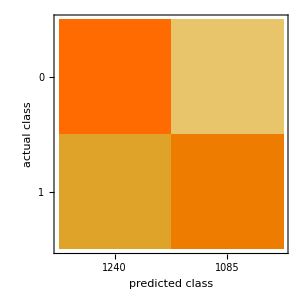
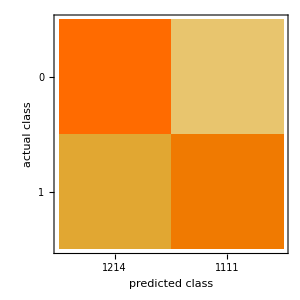
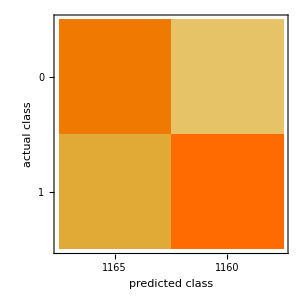
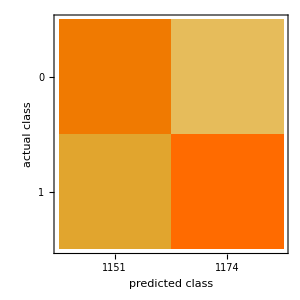
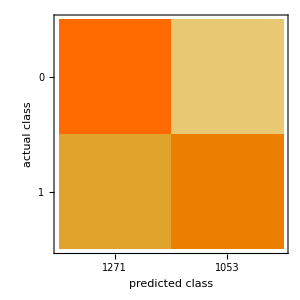

```mathematica
clist={};
accuracylist={};
matthewslist={};
sdlist={};
confmatlist={};
For[i=1,i≤k,i++,
{validation=subset[[i]];
training=Complement[subset//Flatten,validation];
c=Classify[training];
accuracy=ClassifierMeasurements[c,validation,"Accuracy"],
confmat=ClassifierMeasurements[c,validation,"ConfusionMatrixPlot"],
sd=SD[c,validation],
matthews=ClassifierMeasurements[c,validation,"MatthewsCorrelationCoefficient"],
clist=Append[clist,c],
accuracylist=Append[accuracylist,accuracy],
matthewslist=Append[matthewslist,matthews],
sdlist=Append[sdlist,sd],
confmatlist=Append[confmatlist,confmat]
}]
clist
accuracylist
matthewslist
sdlist
confmatlist
```

### If we do not require palindromic coefficients (for non-complete intersections)

```mathematica
hsgennp[datasize_,ifci_,taylororder_:20,max_:{10,10,5}]:=Module[{hslist,counter,numfac,numdegs,num,denomdeg,hs,numexp,coeff},
hslist={};
counter=1;
While[counter≤datasize,
{
numfac=RandomInteger[{1,max[[1]]}];
numdegs=Table[RandomInteger[{1,max[[2]]}],{i,1,numfac}];
num=Times@@((1-t^#)&/@numdegs);
denomdeg=RandomInteger[{1,max[[3]]}]+Total[numdegs];
If[ifci[[counter]]==1,hs=num/(1-t)^denomdeg,hs=(1+Sum[RandomInteger[{-2,2}]t^i,{i,1,max[[2]]}])/(1-t)^denomdeg];
numexp=CoefficientList[Numerator[hs],t];
coeff=Series[hs,{t,0,taylororder}][[3]];
AppendTo[hslist,{hs,numexp,coeff,ifci[[counter]]}];
counter++;
}];
Return[hslist]]
```

```mathematica
datasetnp={};
```

```mathematica
n=15000;
datasetnp=Union[datasetnp,hsgennp[n,{Table[1,{i,1,n/2}],Table[0,{i,1,n/2}]}//Flatten]];
Length[datasetnp]
Count[datasetnp[[;;,4]],0]
Count[datasetnp[[;;,4]],1]
```

12945

7500

5445

```mathematica
n=100;
datasetnp=Union[datasetnp,hsgennp[n,Table[1,{i,1,n}]]];
Length[datasetnp]
Count[datasetnp[[;;,4]],0]
Count[datasetnp[[;;,4]],1]
```

14987

7500

7487

#### Using numerator coefficients as input

```mathematica
datanp=Map[#[[2]]->#[[4]]&,datasetnp];
datanp=DeleteDuplicates[datanp];
Length[datanp]
```

12978

#### Using Taylor coefficients as input

```mathematica
datanp=Map[#[[3]]->#[[4]]&,datasetnp];
datanp=DeleteDuplicates[datanp];
Length[datanp]
```

15002

#### Export data

using numerator coefficients as input

```mathematica
rightpad[x_,n_]:=Block[{res,i},
res=Table[0,{i,1,n}];
Do[res[[i]]=x[[i]],{i,1,Length[x]}];
Return[res];
]
```

```mathematica
datanumnp=Map[{#[[2]],#[[4]]}&,datasetnp];
datanumnp=DeleteDuplicates[datanumnp];
Length[datanumnp]
```

12973

```mathematica
Max[Union[Length[#[[1]]]&/@datanumnp]]
```

88

```mathematica
datanumnppad=rightpad[#[[1]],88]&/@datanumnp;
```

```mathematica
datanumnpinput=Map[{#}&,datanumnppad];
Length[datanumnpinput]
datanumnpoutput=Map[#[[2]]&,datanumnp];
Length[datanumnpoutput]
```

12973

12973

using Taylor coefficients as input

```mathematica
datataynp=Map[{#[[3]],#[[4]]}&,datasetnp];
datataynp=DeleteDuplicates[datataynp];
Length[datataynp]
```

14987

```mathematica
datataynpinput=Map[{#[[1]]}&,datataynp];
Length[datataynpinput]
datataynpoutput=Map[#[[2]]&,datataynp];
Length[datataynpoutput]
```

14987

14987

```mathematica
Export["Directory Here",datanumnpinput];
Export["Directory Here",datanumnpoutput];
Export["Directory Here",datataynpinput];
Export["Directory Here",datataynpoutput];
```

#### Machine Learning

```mathematica
k=5;
subsetnp={};
For[i=1,i≤k,i++,
{If[i≠k,subsetnp=Append[subsetnp,RandomSample[Complement[datanp,subsetnp//Flatten],Round[Length[datanp]/k]]],subsetnp=Append[subsetnp,RandomSample[Complement[datanp,subsetnp//Flatten],Length[datanp]-Round[Length[datanp]/k]*(k-1)]]]
}]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

{0.766,0.764,0.756333,0.758,0.767488}

{<|0→0.54187,1→0.54187|>,<|0→0.536212,1→0.536212|>,<|0→0.536919,1→0.536919|>,<|0→0.520378,1→0.520378|>,<|0→0.5395,1→0.5395|>}

{0.234667,0.238667,0.243667,0.242,0.232512}

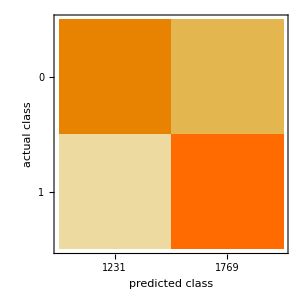
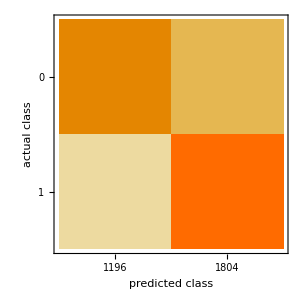
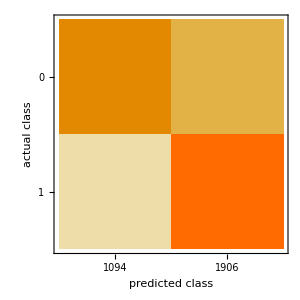
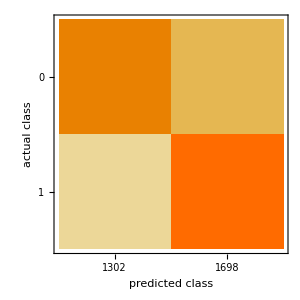
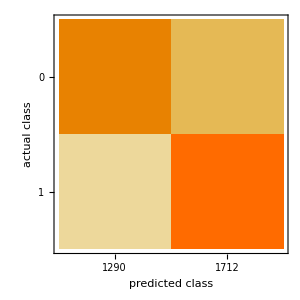

```mathematica
clist={};
accuracylist={};
matthewslist={};
sdlist={};
confmatlist={};
For[i=1,i≤k,i++,
{validation=subsetnp[[i]];
training=Complement[subsetnp//Flatten,validation];
c=Classify[training];
accuracy=ClassifierMeasurements[c,validation,"Accuracy"],
confmat=ClassifierMeasurements[c,validation,"ConfusionMatrixPlot"],
sd=SD[c,validation],
matthews=ClassifierMeasurements[c,validation,"MatthewsCorrelationCoefficient"],
clist=Append[clist,c],
accuracylist=Append[accuracylist,accuracy],
matthewslist=Append[matthewslist,matthews],
sdlist=Append[sdlist,sd],
confmatlist=Append[confmatlist,confmat]
}]
clist
accuracylist
matthewslist
sdlist
confmatlist
```